```mathematica
a={a0,a1,a2};
b={b0,b1,b2};
c={c0,c1,c2};
X={x0,x1,x2};
Simplify[Dot[X-c,Inverse[{a-c,b-c,Cross[a-c,b-c]}]]-Dot[X-c,Inverse[{a-c,b-c,Cross[a-c,b-c]}]]]
```

{0,0,0}

```mathematica
d=Import["/Users/tomoaki/Desktop/static_pressure.csv"][[1]];
Column@Table[{i,d[[i]]},{i,1,Length[d]}]
```

Import::nffil: Importの最中にファイル/Users/tomoaki/Desktop/static_pressure.csvが見付かりませんでした．

Part::partd: 部分指定$Failed⟦1⟧の長さはオブジェクトの深さを超えています．

{1,$Failed}
{2,1}

```mathematica
all =10000;
n=10;
Sum[(n-i)/n*all,{i,0,n}]/Sum[all,{i,0,n}]
```

1/2

### 静水圧データ

```mathematica
ClearAll["Global`*"]
ρ=1000;
g=9.81;
s=0.1;

dataO=Import["/Users/tomoaki/Desktop/static_pressure.csv"];
dataT=Transpose[dataO];
ListPlot[
{Table[{h,ρ*g*(s-h)},{h,0,0.1,0.01}],
Transpose[{dataT[[14]],dataT[[5]]}]},
(*以下はオプション*)
Joined->{True,False},
Frame->True,
FrameStyle->Directive[Black],
FrameLabel->{"Depth [m]","Pressure [Pa]"},
LabelStyle->{FontFamily->"Times",FontSize->20},
FrameTicksStyle->Directive[Black, FontFamily->"Times",FontSize->20],
PlotRange->{{0,0.1},{-100,1100}},
GridLines->Automatic,
PlotStyle->{{Blue,Thick},{Red,Opacity->0.5}},
ImageSize->500
]
```

Import::nffil: Importの最中にファイル/Users/tomoaki/Desktop/static_pressure.csvが見付かりませんでした．

Part::partw: Transpose[$Failed]の部分14は存在しません．

Part::partw: Transpose[$Failed]の部分5は存在しません．

Transpose::nmtx: {Transpose[$Failed]⟦14⟧,Transpose[$Failed]⟦5⟧}の最初の2個のレベルは転置できません．

ListPlot::lpn: {{{0.,981.},{0.01,882.9},{0.02,784.8},{0.03,686.7},{0.04,588.6},{0.05,490.5},{0.06,392.4},{0.07,294.3},{0.08,196.2},{0.09,98.1},{0.1,0.}},{}}は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListPlot::lpnのこれ以上の出力は表示されません．

ListPlot[{{{0.,981.},{0.01,882.9},{0.02,784.8},{0.03,686.7},{0.04,588.6},{0.05,490.5},{0.06,392.4},{0.07,294.3},{0.08,196.2},{0.09,98.1},{0.1,0.}},Transpose[{Transpose[$Failed]⟦14⟧,Transpose[$Failed]⟦5⟧}]},Joined→{True,False},Frame→True,FrameStyle→Directive[GrayLevel[0]],FrameLabel→{Depth [m],Pressure [Pa]},LabelStyle→{FontFamily→Times,FontSize→20},FrameTicksStyle→Directive[GrayLevel[0],FontFamily→Times,FontSize→20],PlotRange→{{0,0.1},{-100,1100}},GridLines→Automatic,PlotStyle→{{RGBColor[0, 0, 1],Thickness[Large]},{RGBColor[1, 0, 0],Opacity→0.5}},ImageSize→500]

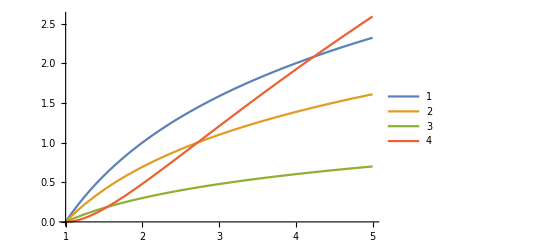

```mathematica
Plot[{Log2[x],Log[x],Log10[x],Log[x]^2},{x,1,5},PlotLegends->Automatic]
```